```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$FAVerbose=1;
SetOptions[InsertFields, Model ->"./modelFiles/SMS-test_FA/SMS-test_FA",GenericModel-> "./modelFiles/SMS-test_FA/Lorentz", InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies];
```

```mathematica
mS1 =  { S[5]} -> {S[5]};
tops = CreateTopologies[1, 1->1];
```

```mathematica
allDiags = InsertFields[tops,mS1, InsertionLevel-> {Particles}];
```

generic model {./modelFiles/SMS-test_FA/Lorentz} initialized

classes model {./modelFiles/SMS-test_FA/SMS-test_FA} initialized

in total: 1 Particles insertion

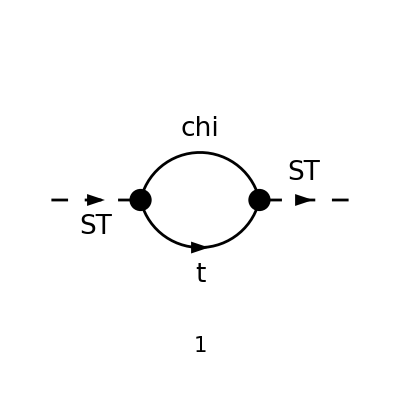

```mathematica
Paint[allDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
diags=DiagramExtract[allDiags,{1}];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1},OutgoingMomenta->{p1},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

(tr((mt-γ·q).(-ⅈ yDM).(mChi+γ·(p1-q)).(-ⅈ yDM)))/((q^2-mt^2).((q-p1)^2-mChi^2))

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[0]]]
```

-(4 yDM^2 (mChi mt-p1·q+q^2))/((q^2-mt^2).((p1-q)^2-mChi^2))

```mathematica
ChangeDimension
```

```mathematica
amp[3]=TID[amp[2],q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

-2 ⅈ π^2 yDM^2 (((mChi+mt)^2-p1^2) B_0(p1^2,mChi^2,mt^2)+A_0(mChi^2)+A_0(mt^2))

```mathematica
(* Make sure there are no divergences *)
UVpart = Simplify[DiracSimplify[PaXEvaluateUV[amp[3]]]]
```

-(2 ⅈ π^2 yDM^2 (2 (mChi^2+mChi mt+mt^2)-p1^2))/ε_UV

```mathematica
ampAll=Simplify[PaXEvaluate[amp[3],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions->{mt>0,mChi>0}]
```

1/(16 π^2 ε p1^2)ⅈ yDM^2 (2 p1^2 (-ε mChi^2 log(μ^2/(π mChi^2))-3 ε mChi^2+2 ℽ ε mChi^2-4 ε mChi^2 log(2 π)+ε mChi^2 log(π)+ε mt (mChi+mt) log(mChi^2/mt^2)+ε √(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4)+mChi^2+mt^2-p1^2)/(2 mChi mt))-2 mChi^2-ε (mChi+mt)^2 log(μ^2/mt^2)-4 ε mChi mt+2 ℽ ε mChi mt-4 ε mChi mt log(2 π)+2 ε mChi mt log(π)-2 mChi mt-ε mt^2 log(μ^2/(π mt^2))-3 ε mt^2+2 ℽ ε mt^2-4 ε mt^2 log(2 π)+ε mt^2 log(π)-2 mt^2)+ε (mChi+mt)^2 ((mChi^2-mt^2) log(mChi^2/mt^2)-2 √(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4)+mChi^2+mt^2-p1^2)/(2 mChi mt)))+p1^4 (2 ε log(μ^2)-2 ℽ ε+4 ε+2 ε log(π)+ε log(16)-2 ε log(mChi)-2 ε log(mt)+2))

```mathematica
Series[ampAll,{Epsilon,0,0}]
```

(ⅈ yDM^2 (-2 mChi^2-2 mChi mt-2 mt^2+p1^2))/(8 π^2 ε)+1/(16 π^2 p1^2)ⅈ yDM^2 (2 p1^2 (mChi^2 (-log(μ^2/(π mChi^2)))+√(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4)+mChi^2+mt^2-p1^2)/(2 mChi mt))+mt (mChi+mt) log(mChi^2/mt^2)+2 ℽ mChi^2-3 mChi^2-4 mChi^2 log(2 π)+mChi^2 log(π)-(mChi+mt)^2 log(μ^2/mt^2)+2 ℽ mChi mt-4 mChi mt-4 mChi mt log(2 π)+2 mChi mt log(π)-mt^2 log(μ^2/(π mt^2))+2 ℽ mt^2-3 mt^2-4 mt^2 log(2 π)+mt^2 log(π))+(mChi+mt)^2 ((mChi^2-mt^2) log(mChi^2/mt^2)-2 √(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mt^2)+(mChi^2-mt^2)^2+p1^4)+mChi^2+mt^2-p1^2)/(2 mChi mt)))+p1^4 (2 log(μ^2)-2 log(mChi)-2 log(mt)-2 ℽ+4+2 log(π)+log(16)))+O(ε^1)

```mathematica
InputForm[%]
```

((I/16)*yDM^2*((2 + 4*Epsilon - 2*Epsilon*EulerGamma + Epsilon*Log[16] - 2*Epsilon*Log[mChi] - 2*Epsilon*Log[mt] + 2*Epsilon*Log[Pi] + 2*Epsilon*Log[ScaleMu^2])*
    Pair[Momentum[p1, D], Momentum[p1, D]]^2 + Epsilon*(mChi + mt)^2*((mChi^2 - mt^2)*Log[mChi^2/mt^2] - 
     2*Log[(mChi^2 + mt^2 - Pair[Momentum[p1, D], Momentum[p1, D]] + Sqrt[(mChi^2 - mt^2)^2 - 2*(mChi^2 + mt^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
           Pair[Momentum[p1, D], Momentum[p1, D]]^2])/(2*mChi*mt)]*Sqrt[(mChi^2 - mt^2)^2 - 2*(mChi^2 + mt^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
        Pair[Momentum[p1, D], Momentum[p1, D]]^2]) + 2*Pair[Momentum[p1, D], Momentum[p1, D]]*(-2*mChi^2 - 3*Epsilon*mChi^2 + 2*Epsilon*EulerGamma*mChi^2 - 
     2*mChi*mt - 4*Epsilon*mChi*mt + 2*Epsilon*EulerGamma*mChi*mt - 2*mt^2 - 3*Epsilon*mt^2 + 2*Epsilon*EulerGamma*mt^2 + Epsilon*mt*(mChi + mt)*Log[mChi^2/mt^2] + 
     Epsilon*mChi^2*Log[Pi] + 2*Epsilon*mChi*mt*Log[Pi] + Epsilon*mt^2*Log[Pi] - 4*Epsilon*mChi^2*Log[2*Pi] - 4*Epsilon*mChi*mt*Log[2*Pi] - 
     4*Epsilon*mt^2*Log[2*Pi] - Epsilon*(mChi + mt)^2*Log[ScaleMu^2/mt^2] - Epsilon*mChi^2*Log[ScaleMu^2/(mChi^2*Pi)] - Epsilon*mt^2*Log[ScaleMu^2/(mt^2*Pi)] + 
     Epsilon*Log[(mChi^2 + mt^2 - Pair[Momentum[p1, D], Momentum[p1, D]] + Sqrt[(mChi^2 - mt^2)^2 - 2*(mChi^2 + mt^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
           Pair[Momentum[p1, D], Momentum[p1, D]]^2])/(2*mChi*mt)]*Sqrt[(mChi^2 - mt^2)^2 - 2*(mChi^2 + mt^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
        Pair[Momentum[p1, D], Momentum[p1, D]]^2])))/(Epsilon*Pi^2*Pair[Momentum[p1, D], Momentum[p1, D]])

```mathematica
Limit[%,mChi-> mST]
```

1/(s ε)aS yDM^2 ((-ⅈ mST^4 ε ((γ·(k1-p2)).(γ̄)^6 (-2 log(1/mST)-4 log(mST)-2 log(mST^2)+log(mST^6)) (T^Glu1 T^Glu2)_Col4Col3+(γ·(k2-p2)).(γ̄)^6 (4 log(1/mST)+2 log(mST)-log(mST^2)+4 log(ⅈ μ)-4 log((2 ⅈ μ)/mST)+log(16)) (T^Glu2 T^Glu1)_Col4Col3)) ∞)

```mathematica
Factor[Expand[%43]]
```

1/(96 π mST^2)ⅈ aS yDM^2 (7 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-7 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-5 (γ·p1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+4 (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+5 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)

```mathematica
Collect[Expand[%43],DiracGamma[x_,D]]
```

(7 ⅈ aS yDM^2 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(5 ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)+(ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(24 π mST^2)-(ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(24 π mST^2)+(5 ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)

```mathematica
Collect[Expand[%43]/.{DiracGamma[Momentum[x_,D],D].DiracGamma[6]-> GS[x] Subscript[P, L]},{GS[p1],GS[p2],GS[k1],GS[k2]},Simplify]
```

(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k1] (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k2] (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p1] (5 (T^Glu1 T^Glu2)_Col4Col3-4 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p2] (4 (T^Glu1 T^Glu2)_Col4Col3-5 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)